## Comparing the nuc & cyto intensity measurements of fix cell accumulation 15h experiments

### Importing files... CHOOSE ONE DAY ONLY!

Import the csv file from Measure_cyto_nuc_bkg_AutoThreshold.ijm processed fix cell images, stained with Cy3-FLAG-Fab

#### 03/30 -BoxB 15h: 1B = TA 2B = NT 3B = TL

```mathematica
myOrderOfFiles = {2,3,1};
```

```mathematica
(*Update fle loc*)myFileTL3=FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3*/*5*/R*3b.csv"]
myFileNT3 = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3*/*5*/R*2b.csv"]
myFileTA3 =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3*/*5*/R*1b.csv"]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Results_3b.csv}

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Results_2b.csv}

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Results_1b.csv}

```mathematica
myFileNames = Flatten@{myFileNT3, myFileTL3, myFileTA3};
dishType = "-BoxB 15h ctrl cells";
```

```mathematica
myAnalysisFolder= "/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/

```mathematica
logfiles = 
Flatten@Table[ 
FileNames[ myAnalysisFolder<>"Log_*"<>ToString[myOrderOfFiles[[i]]]<>"b.txt" ] ,{i,1,3}]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Log_2b.txt,/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Log_3b.txt,/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Log_1b.txt}

```mathematica
mylogs = Import/@logfiles//StringSplit/@#&;
```

Use this line to put the logs in teh right order!! It’ll change with each day experiment, since the files are in different orders......

The following two dimensions MUST MATCH to make the data frame!!

```mathematica
Dimensions/@mylogs
Dimensions/@a00
```

{{109},{117},{180}}

{{64},{35},{56}}

#### 03/30 +BoxB, 24h: 4B = TL 5B = NT 6B = TA

```mathematica
myOrderOfFiles = {5,4,6};
myAnalysisFolder= "/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/";
```

```mathematica
myFileNT4= FileNames[myAnalysisFolder<>"R*"<>ToString[myOrderOfFiles[[1]]]<>"b*.csv"]
myFileTL4 = FileNames[myAnalysisFolder<>"R*"<>ToString[myOrderOfFiles[[2]]]<>"b*.csv"]
myFileTA4 =FileNames[myAnalysisFolder<>"R*"<>ToString[myOrderOfFiles[[3]]]<>"b*.csv"]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Results_5b.csv}

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Results_4b.csv}

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Results_6b.csv}

```mathematica
myFileNames = Flatten@{myFileNT4, myFileTL4,myFileTA4};
dishType = "+BoxB 24h cells";
```

```mathematica
logfiles = 
Flatten@Table[ 
FileNames[ myAnalysisFolder<>"Log_*"<>ToString[myOrderOfFiles[[i]]]<>"b.txt" ] ,{i,1,3}]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Log_5b.txt,/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Log_4b.txt,/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/Fix_accum_cy3FLAGFab_wwoBoxB_5/Log_6b.txt}

```mathematica
mylogs = Import/@logfiles//StringSplit/@#&;
```

Use this line to put the logs in teh right order!! It’ll change with each day experiemnt, since the files are in different orders......

```mathematica
(*mylogs = {mylogs0[[3]],mylogs0[[1]],mylogs0[[2]]};
```

```mathematica
Dimensions/@a00
```

{{35},{64},{56}}

```mathematica
mylogs[[2,1]]
```

4b000.tif

```mathematica
Length/@mylogs
Length/@a00
```

{64,35,56}

{35,64,56}

## Running the code

### Make Nuc/whole cell intensity graphs to visualize data... Use this section to check on your spread of background intensities, and check out the ch1 and ch2 intensities plotted generous vs conservative measurement strategies JUST for visualization purposes

```mathematica
mycsv = Import /@myFileNames;
mycsv[[1,1]]
Length@mycsv
(*CSV Files:   NT, TL, TA*)
```

{,Area,Mean,Min,Max}

3

```mathematica
mymsrmts = Table[ Partition[ Flatten@mycsv[[i, 2;;All]] , 8(*4 bkgd, 2 nuc, 2 cyto*) *5 (*5 measureents, {"","Area","Mean","Min","Max"}*)]  ,{i,1,Length@mycsv,1}];
ncells = Length/@mymsrmts
```

{109,117,180}

```mathematica
myAreas = Table[ mymsrmts[[i,All,2;;All;;5]], {i,1,Length@mymsrmts}];
myMeans = Table[ mymsrmts[[i,All,3;;All;;5]],  {i,1,Length@mymsrmts}];
myMaxs = Table[ mymsrmts[[i,All,5;;All;;5]],  {i,1,Length@mymsrmts}];
```

```mathematica
ch1bkgs =  Table[ myMeans[[i,All,1;;2]], {i,1,Length@mymsrmts}];
meanCh1bkgs =  Table[ Min/@ch1bkgs[[i]] , {i,1,Length@mymsrmts}];
ch2bkgs =  Table[ myMeans[[i,All,3;;4]], {i,1,Length@mymsrmts}];
meanCh2bkgs =  Table[ Min/@ch2bkgs[[i]] , {i,1,Length@mymsrmts}];
```

Plots comparing the background at each corner...

Backgorund top corner vs background bottom corner

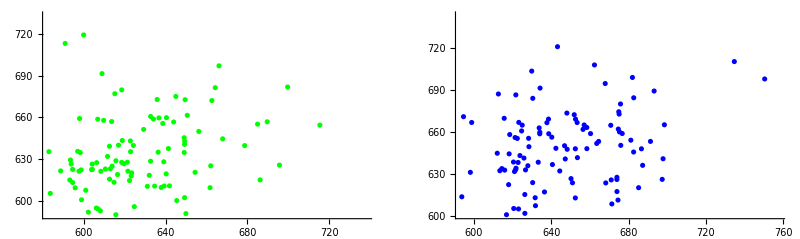
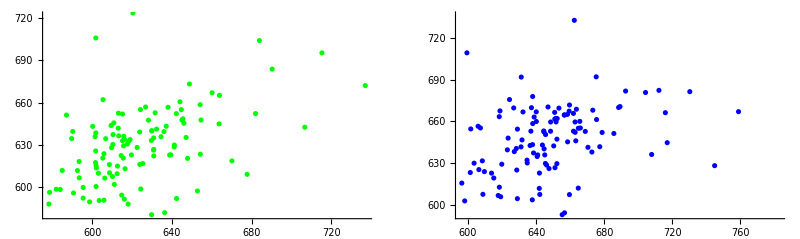
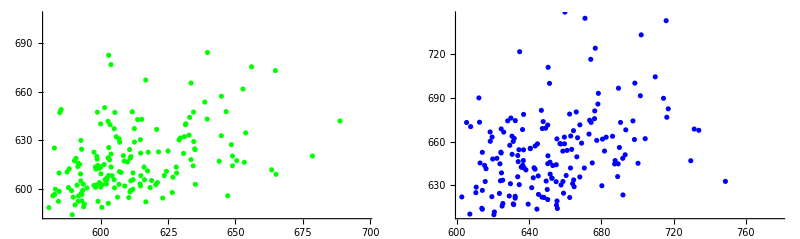

```mathematica
"Backgorund top corner vs background bottom corner"
Table[ GraphicsRow[{ ListPlot[ch1bkgs[[i]], PlotStyle->Green],
ListPlot[ch2bkgs[[i]], PlotStyle->Blue]   }], {i,1,Length@mymsrmts}]
```

```mathematica
ch1nuccyto= Table[ myMeans[[i, All,5;;6]] , {i,1,Length@mymsrmts}];
ch2nuccyto = Table[ myMeans[[i, All,7;;8]] , {i,1,Length@mymsrmts}];
```

Plots comparing the Nuc/Cyto ratios, to try to find out which measurement is better or more accurate:

{{109  cells measured,117  cells measured,180  cells measured}}

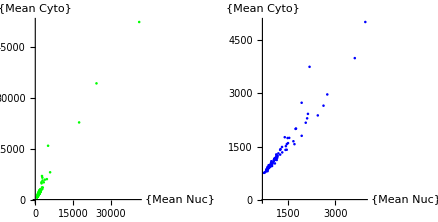
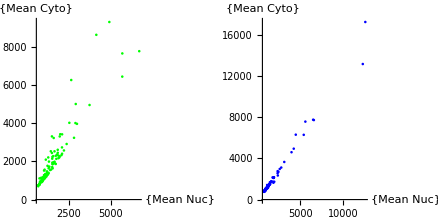
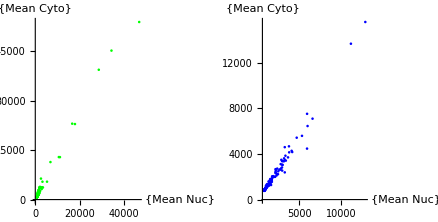

```mathematica
myPlotOptions = { AspectRatio-> 1, PlotRange->All, ImageSize-> 200, LabelStyle->{FontFamily->"Arial Narrow",14,GrayLevel[0]},   AxesLabel->{{"Mean Nuc"},{"Mean Cyto"}}}   ;

{ ncells  " cells measured"}

mynuccellgraphs = Table[ GraphicsRow[{   ListPlot[ch1nuccyto[[i]], PlotStyle->Green, myPlotOptions[[All]] ],
ListPlot[ch2nuccyto[[i]], PlotStyle->Blue, myPlotOptions[[All]] ]   
}] ,  {i,1,Length@mymsrmts}]
```

### Set parameters and define dataset as a00 NOTE: Manual step adds

#### Parameters...

```mathematica
myfont = BaseStyle->{FontFamily->"Arial Narrow",FontSize->22};
```

```mathematica
l=.4; m=.1; (*how wide your data is on your box/whisker plot*)
s=.0175; (*Size of plot markers*)
```

b =   ListPlot 
a =   data

```mathematica
boxWhiskStyleLog = {
{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}} 
};
```

```mathematica
boxWhiskStyle = {
{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } ,ChartLabels->{"Non-Tetherable","Tetherable LacZ","Tetherable AGO"},  AspectRatio->1 , {Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}} 
};
```

#### Remove Background (Subtract)

```mathematica
bkgdSubtractValue = 0;
```

```mathematica
(*bkgdSubtractValue = Which[dishType == "-BoxB ctrl cells", 24,
dishType == "+BoxB cells",189,
dishType =!  "+BoxB cells", 0];
```

```mathematica
bkgdSubtractValue
```

0

```mathematica
a00 = ch1nuccyto[[All,All,2]] - meanCh1bkgs -bkgdSubtractValue;
c00 = ch2nuccyto[[All,All,2]] - meanCh2bkgs -bkgdSubtractValue;
Min/@a00
Min/@c00
```

{94.954,68.992,53.436}

{92.918,97.013,138.423}

NOTE!!! You can use either 1 or 2. These two different measurements are either the NUC or NUC+CYTO. They should give ~same results....

#### Remove duplicates...

```mathematica
deleteDuplicateNucIntensities = DeleteDuplicates/@Sort/@Table[Table[SetPrecision[a00[[cell,ints]],3],{ints,1,Length@a00[[cell]]}],{cell,1,Length@a00}];
Length/@deleteDuplicateNucIntensities
DeleteDuplicates/@a00//Length/@#&
{" The # of removed duplicates =  " , (Length/@deleteDuplicateNucIntensities) - (DeleteDuplicates/@a00//Length/@#&)}
```

{103,115,167}

{109,116,180}

{ The # of removed duplicates =  ,{-6,-1,-13}}

### Not used! Plots in linear and log scale of cy3 accumulation in the nucleus (ALSO calculated below from dataframe)

#### Log scale...

Use this line to use ALL cells, no deleted duplicates:

```mathematica
(* a = a00*)
```

Use this line to use non-duplicated cells:

```mathematica
a=a00;
Length/@a00
```

{64,35,56}

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , ScalingFunctions->"Log2" ,PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
```

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
```

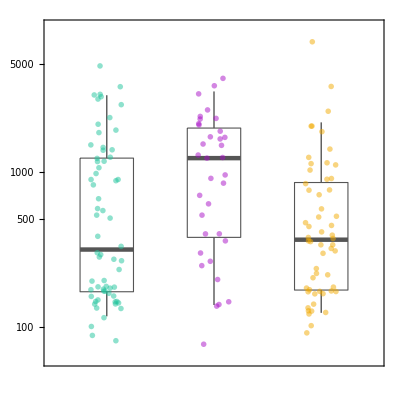

```mathematica
Show[   bwchart,b, AspectRatio -> 1,myfont]
```

#### Linear scale...

Use this line to use ALL cells, no deleted duplicates:

```mathematica
(* a = a00*)
```

Use this line to use non-duplicated cells:

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ];
```

```mathematica
bwchart = BoxWhiskerChart[a, { {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,PlotRange-> {0,8000},  ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
```

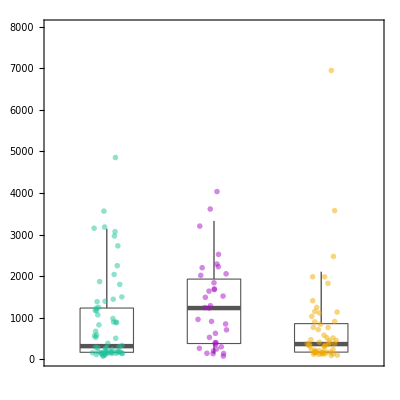

```mathematica
Show[   bwchart,b, AspectRatio -> 1,myfont]
```

#### Counts, Means & Standard Deviations

```mathematica
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  } //TableForm
```

64 | 35 | 56
317.484 | 1233.31 | 367.188
1052.62 | 1039.87 | 1080.95

#### MannWhitney Tests...

```mathematica
3*{  MannWhitneyTest[ {a[[1]],a[[3]]} ]    ,(*TA?*)
MannWhitneyTest[ {a[[2]],a[[3]]} ]   , (*TA?*)
MannWhitneyTest[ {a[[1]],a[[2]]} ]   }
```

{2.28688,0.00498601,0.0380858}

#### Cumulative Plots:

#### Kolm-Smirnov tests...

```mathematica
{KolmogorovSmirnovTest[a[[1]],a[[3]] ],
KolmogorovSmirnovTest[a[[1]],a[[2]] ],
KolmogorovSmirnovTest[a[[2]],a[[3]] ]}*3
```

{1.28727,0.098644,0.0111649}

#### End

## -BoxB controls NT, TL, &TA: Make data frame, add

Check to make sure your # of cells match before continuing!

```mathematica
Length/@mylogs
Length/@a00
```

{109,117,180}

{109,117,180}

```mathematica
mycells0 = Table[Table[Import[myAnalysisFolder <>mylogs[[type,cell]]  ] , {cell,1,Length@mylogs[[type]], 1}],{type,1,3}];
Dimensions/@mycells0
```

{{109,2},{117,2},{180,2}}

```mathematica
mycells = Table[ Table[ ImageResize[#,{128,128}]&/@mycells0[[type,cell]],{cell, 1, Length@mycells0[[type]]}],{type, 1, 3}];
ImageAdjust/@mycells[[1,1]]
```

{-Graphics-,-Graphics-}

```mathematica
dataFrame =  Table[Table[ Join[ { mylogs[[i,j]]}, mycells[[i,j]]  ,{meanCh1bkgs[[i,j]] ,  meanCh2bkgs[[i,j]] } ,ch1nuccyto[[i,j]]  ,ch2nuccyto [[i,j]]  ,
ch1nuccyto[[i,j]] -meanCh1bkgs[[i,j]]   ,ch2nuccyto [[i,j]]  -meanCh2bkgs[[i,j]] 
],{j,1,Length@mycells[[i]]}],{i,1,3}];
```

```mathematica
dataFrame[[1,1]]
Dimensions/@dataFrame
```

{2b001.tif,-Graphics-,-Graphics-,608.242,625.977,5865.5,8045.14,1670.7,1648.99,5257.25,7436.9,1044.73,1023.01}

{{109,13},{117,13},{180,13}}

```mathematica
mylabels = { "Image File" ,"Cell Image Ch1 Cy3" ,"Cell Image Ch2 GFP" ,"Ch1 bkg" ,"Ch2 bkg" ,"Mean Ch1 Intensity (conservative)" ,"Mean Ch1 Intensity (generous)"  ,"Mean Ch2 Intensity (conservative)" ,"Mean Ch2 Intensity (generous)" ,
"Mean Ch1 Intensity (conservative) - bkg" ,"Mean Ch1 Intensity (generous) - bkg"  ,"Mean Ch2 Intensity (conservative) - bkg" ,"Mean Ch2 Intensity (generous) - bkg"}//TableForm
```

Image File
Cell Image Ch1 Cy3
Cell Image Ch2 GFP
Ch1 bkg
Ch2 bkg
Mean Ch1 Intensity (conservative)
Mean Ch1 Intensity (generous)
Mean Ch2 Intensity (conservative)
Mean Ch2 Intensity (generous)
Mean Ch1 Intensity (conservative) - bkg
Mean Ch1 Intensity (generous) - bkg
Mean Ch2 Intensity (conservative) - bkg
Mean Ch2 Intensity (generous) - bkg

### Plots:

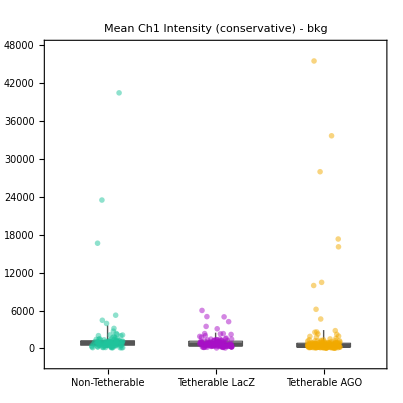

109 | 117 | 180
871.91 | 621.579 | 417.496
4645.78 | 991.616 | 5021.96
2.40521×10^-7 | 0.00027688 | 0.0607749

```mathematica
a=Table[dataFrame[[type,All,10]],{type,1,3}];b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
a//Show[BoxWhiskerChart[#,boxWhiskStyle[[1]],boxWhiskStyle[[2;;All]] ,PlotLabel->mylabels[[1,10]] , myfont   ]   ,b]& 
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  ,{  MannWhitneyTest[ {a[[1]],a[[3]]} ]    ,(*TA?*)
MannWhitneyTest[ {a[[2]],a[[3]]} ]   , (*TA?*)
MannWhitneyTest[ {a[[1]],a[[2]]} ]   }} //TableForm
```

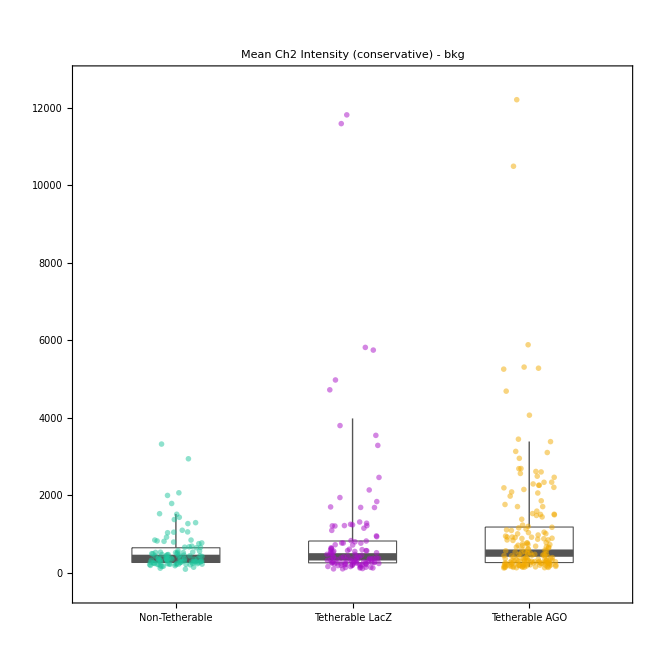

109 | 117 | 180
368.663 | 408.376 | 504.185
530.537 | 1784.57 | 1550.17
0.059627 | 0.552375 | 1.19105

```mathematica
c=12;
a=Table[dataFrame[[type,All,c]],{type,1,3}];b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
a//Show[BoxWhiskerChart[#,boxWhiskStyle[[1]],boxWhiskStyle[[2;;All]] ,PlotLabel->mylabels[[1,c]] , myfont ],  b]& 
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  ,3*{  MannWhitneyTest[ {a[[1]],a[[3]]} ]    ,(*TA?*)
MannWhitneyTest[ {a[[2]],a[[3]]} ]   , (*TA?*)
MannWhitneyTest[ {a[[1]],a[[2]]} ]   }} //TableForm
```

MWW’s bonferroni correction??

#### extra:

```mathematica
mylabels[[1,12]]
```

Mean Ch2 Intensity (conservative) - bkg

```mathematica
(* 3b, 1b, 2b*)
```

```mathematica
dataFrame[[3,1]]
```

{1b000.tif,-Graphics-,-Graphics-,584.211,615.694,997.053,1090.31,2469.85,2478.02,412.842,506.095,1854.15,1862.33}

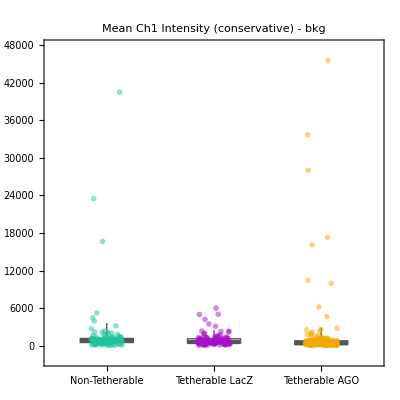

```mathematica
a=Table[dataFrame[[type,All,10]],{type,1,3}];b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
a//Show[BoxWhiskerChart[#,boxWhiskStyle[[1]],boxWhiskStyle[[2;;All]] ,PlotLabel->mylabels[[1,10]] ]   ,b]&
```

```mathematica
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  } //TableForm
```

109 | 117 | 180
871.91 | 621.579 | 417.496
4645.78 | 991.616 | 5021.96

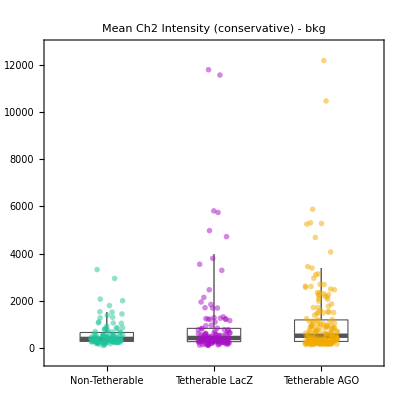

109 | 117 | 180
368.663 | 408.376 | 504.185
530.537 | 1784.57 | 1550.17

```mathematica
c=12;
a=Table[dataFrame[[type,All,c]],{type,1,3}];b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
a//Show[BoxWhiskerChart[#,boxWhiskStyle[[1]],boxWhiskStyle[[2;;All]] ,PlotLabel->mylabels[[1,c]] ]   ,b]& 
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  } //TableForm
```

```mathematica
(*These are #,Med,Stdev for -BoxBs!*) {{177, 150, 142}, {862.473, 427.429, 559.8185}, {1623.5633295278583, 618.5926259201404, 755.1807979881027}}
```

{{177,150,142},{862.473,427.429,559.819},{1623.56,618.593,755.181}}

#### Looking at cutoffs for GFP signal -> Does the level of GFP in the cells affect the amount of accumulation? Do only the bright GFP cells have accumulation?

JUST the cells with greater than 500 mean GFP signal...

```mathematica
cutoff = 500;
tempdata = Table[ Cases[dataFrame[[type]], x_ /; x[[gfp]]>cutoff] ,{type,1,3}] ;
Mean/@ tempdata[[All,All,cy3]]
BoxWhiskerChart[ tempdata[[All,All,cy3]] ]
```

Part::pkspec1: The expression gfp cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression cy3 cannot be used as a part specification.

Part::pkspec1: The expression Mean[All] cannot be used as a part specification.

{}⟦Mean[All],Mean[All],Mean[cy3]⟧

Part::pkspec1: The expression cy3 cannot be used as a part specification.

BoxWhiskerChart::ldata: {{},{},{}}⟦All,All,cy3⟧ is not a valid dataset or list of datasets.

BoxWhiskerChart[{{},{},{}}⟦All,All,cy3⟧]

```mathematica
(*TL, TA, NT*)
```

Part::pkspec1: The expression gfp cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression cy3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Median[{{},{},{},{},{}}⟦1,All,cy3⟧] | Median[{{},{},{},{},{}}⟦1,All,cy3⟧] | Median[{{},{},{},{},{}}⟦1,All,cy3⟧]
Median[{{},{},{},{},{}}⟦2,All,cy3⟧] | Median[{{},{},{},{},{}}⟦2,All,cy3⟧] | Median[{{},{},{},{},{}}⟦2,All,cy3⟧]
Median[{{},{},{},{},{}}⟦3,All,cy3⟧] | Median[{{},{},{},{},{}}⟦3,All,cy3⟧] | Median[{{},{},{},{},{}}⟦3,All,cy3⟧]
Median[{{},{},{},{},{}}⟦4,All,cy3⟧] | Median[{{},{},{},{},{}}⟦4,All,cy3⟧] | Median[{{},{},{},{},{}}⟦4,All,cy3⟧]
Median[{{},{},{},{},{}}⟦5,All,cy3⟧] | Median[{{},{},{},{},{}}⟦5,All,cy3⟧] | Median[{{},{},{},{},{}}⟦5,All,cy3⟧]

Part::pkspec1: The expression cy3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

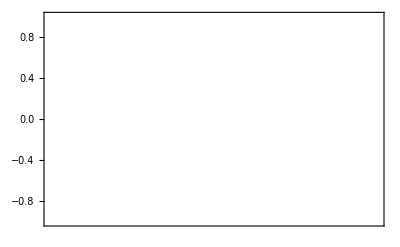
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cutoff = {0,250,500,1000, 2000};
tempdata = Table[Table[ Cases[dataFrame[[type]], x_ /; x[[gfp]]>cutoff[[i]]]  ,{i,1,Length@cutoff}], {type,1,3}] ; 
(*Above, data from the cutoff, Below, picking just the cy3 signals based on those cutoff cells....*)
tempdata1=Table[ tempdata [[ type ]][[i,All,cy3]] , {i,1,Length@cutoff}  ,{type,1,3}] ;
Table[ Median/@tempdata1[[i]],{i,1,Length@cutoff}] //TableForm
tempdata1// BoxWhiskerChart/@#&
```

#### Next

### Adding IMAGES and LOGS, + BoxB:

### Median cell images

```mathematica
mylabels
```

Image File
Cell Image Ch1 Cy3
Cell Image Ch2 GFP
Ch1 bkg
Ch2 bkg
Mean Ch1 Intensity (conservative)
Mean Ch1 Intensity (generous)
Mean Ch2 Intensity (conservative)
Mean Ch2 Intensity (generous)
Mean Ch1 Intensity (conservative) - bkg
Mean Ch1 Intensity (generous) - bkg
Mean Ch2 Intensity (conservative) - bkg
Mean Ch2 Intensity (generous) - bkg

```mathematica
dataFrame[[1,1,10;;12;;2]]
```

{310.125,1292.16}

```mathematica
dataFrameSorted= Table[ SortBy [ dataFrame[[type]], #[[10]] & ],{type, 1, 3}];
Table[  dataFrameSorted[[type, 1;;All;;20, 2]] , {type,1,3}]; (*shows that cells are in order*)
```

```mathematica
mymediancells = Table[ dataFrameSorted[[type , Round[ Length@dataFrameSorted[[type]]/2 ], 2;;3]] , {type,1,3}]
 Table[ dataFrameSorted[[type , Round[  Length@dataFrameSorted[[type]]/2 ],1]] , {type,1,3}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{3b084.tif,1b053_bright_contam.tif,2b016.tif}

```mathematica
mychannel = 1;
Table[ImageResize[ImageAdjust[mymediancells[[img,mychannel]],{0,0,1},{.001,.2}],{2*64,2*64}],{img,1,3,1}]
```

{-Graphics-,-Graphics-,-Graphics-}

Cy3 cell sorted grid of ALL cells

{100,100,100}

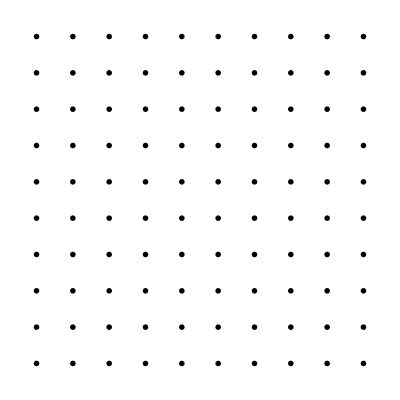
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
mychannel = 1; (*PICK channel you want to look at!!! CH1 = green, CH2 = Blue *)
meanImgs100 = RandomSample[#,100]&/@dataFrameSorted ;
meanImgs100Sorted = Table[ SortBy [ meanImgs100[[type]], #[[10]] & ],{type, 1, 3}]; 
(*LINE of data table...*)
Length/@meanImgs100Sorted
meanImgs100SortedAdjusted = Table[ ImageAdjust[#,{0,1,1},{.00001,.3} ]&/@ meanImgs100Sorted[[type]][[All,mychannel+1]],{type,1,3}];  (*Image adjust *)  
 myGrids = GraphicsGrid[Partition[#,10]]&/@meanImgs100SortedAdjusted
```

```mathematica
meanImgs100SortedAdjusted;
myCellsGsortedAvocado = Table[ Colorize[#,ColorFunction->"AvocadoColors",ColorFunctionScaling->False ]&/@meanImgs100SortedAdjusted[[type]] ,{type, 1,3}];
myGrid = GraphicsGrid[Partition[#,10]]&/@myCellsGsortedAvocado
```

{-Graphics-,-Graphics-,-Graphics-}

## +BoxB NT, TL, &TA:

```mathematica
(*Make sure this line works!! Changed not yet tested!!*)
```

```mathematica
mycells = Table[Table[Import[myAnalysisFolder <>mylogs[[type,cell]]  ] , {cell,1,Length@mylogs[[type]], 1}],{type,1,3}];
Dimensions/@mycells
```

{{64,2},{35,2},{56,2}}

```mathematica
ImageAdjust/@mycells[[1,1]]
```

{-Graphics-,-Graphics-}

```mathematica
Length@ ch1nuccyto[[i]]
Length@ mycells[[i]]
```

64

64

```mathematica
i=1;j=2;    ch1nuccyto[[i,j]] -meanCh1bkgs[[i,j]]
```

{637.746,1171.98}

```mathematica
j=36;{{meanCh1bkgs[[i,j]] ,  meanCh2bkgs[[i,j]] } ,ch1nuccyto[[i,j]]  ,ch2nuccyto [[i,j]]  ,
ch1nuccyto[[i,j]] -meanCh1bkgs[[i,j]]   ,ch2nuccyto [[i,j]]  -meanCh2bkgs[[i,j]] }
```

{{662.084,637.09},{4048.77,5515.48},{1755.64,2019.24},{3386.68,4853.4},{1118.55,1382.15}}

```mathematica
dataFrame =  Table[Table[ Join[ { mylogs[[i,j]]}, mycells[[i,j]]  ,{meanCh1bkgs[[i,j]] ,  meanCh2bkgs[[i,j]] } ,ch1nuccyto[[i,j]]  ,ch2nuccyto [[i,j]]  ,
ch1nuccyto[[i,j]] -meanCh1bkgs[[i,j]]   ,ch2nuccyto [[i,j]]  -meanCh2bkgs[[i,j]] 
],{j,1,Length@mycells[[i]]}],{i,1,3}];
```

```mathematica
dataFrame[[1,1]]
Dimensions/@dataFrame
```

{5b01.tif,-Graphics-,-Graphics-,598.604,601.678,1192.53,1994.47,1057.14,1034.35,593.924,1395.87,455.463,432.671}

{{64,13},{35,13},{56,13}}

```mathematica
mylabels = { "Image File" ,"Cell Image Ch1 Cy3" ,"Cell Image Ch2 GFP" ,"Ch1 bkg" ,"Ch2 bkg" ,"Mean Ch1 Intensity (conservative)" ,"Mean Ch1 Intensity (generous)"  ,"Mean Ch2 Intensity (conservative)" ,"Mean Ch2 Intensity (generous)" ,
"Mean Ch1 Intensity (conservative) - bkg" ,"Mean Ch1 Intensity (generous) - bkg"  ,"Mean Ch2 Intensity (conservative) - bkg" ,"Mean Ch2 Intensity (generous) - bkg"}//TableForm
```

Image File
Cell Image Ch1 Cy3
Cell Image Ch2 GFP
Ch1 bkg
Ch2 bkg
Mean Ch1 Intensity (conservative)
Mean Ch1 Intensity (generous)
Mean Ch2 Intensity (conservative)
Mean Ch2 Intensity (generous)
Mean Ch1 Intensity (conservative) - bkg
Mean Ch1 Intensity (generous) - bkg
Mean Ch2 Intensity (conservative) - bkg
Mean Ch2 Intensity (generous) - bkg

### Plots:

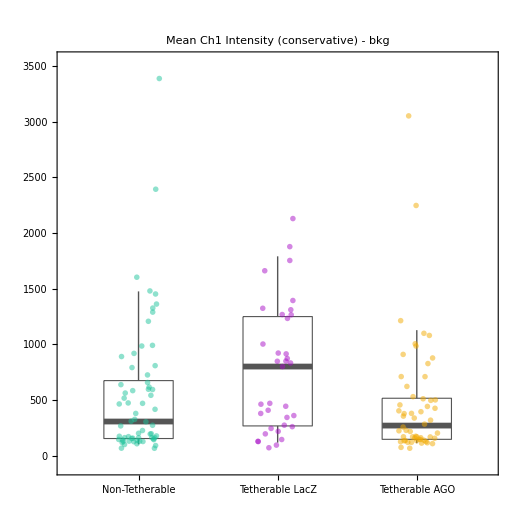

64 | 35 | 56
306.467 | 800.166 | 270.06
597.207 | 572.709 | 527.712
0.48252 | 0.00373081 | 0.0239464

```mathematica
a=Table[dataFrame[[type,All,10]],{type,1,3}];b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
a//Show[BoxWhiskerChart[#,boxWhiskStyle[[1]],boxWhiskStyle[[2;;All]] ,PlotLabel->mylabels[[1,10]] , myfont]   ,b]& 
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  ,{  MannWhitneyTest[ {a[[1]],a[[3]]} ]    ,(*TA?*)
MannWhitneyTest[ {a[[2]],a[[3]]} ]   , (*TA?*)
MannWhitneyTest[ {a[[1]],a[[2]]} ]   }} //TableForm
```

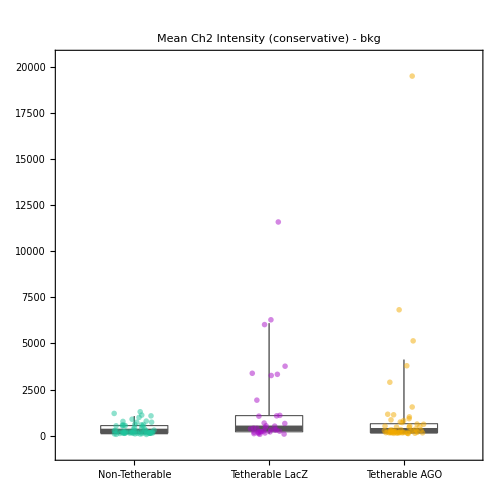

64 | 35 | 56
229.719 | 400.502 | 267.819
308.19 | 2400.31 | 2792.09
0.214793 | 0.50024 | 0.0373081

```mathematica
c=12;
a=Table[dataFrame[[type,All,c]],{type,1,3}];b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
a//Show[BoxWhiskerChart[#,boxWhiskStyle[[1]],boxWhiskStyle[[2;;All]] ,PlotLabel->mylabels[[1,c]] , myfont ],  b]& 
{ N@ Length/@a  , 
N@ Median/@a  , 
 N@StandardDeviation/@a  ,3*{  MannWhitneyTest[ {a[[1]],a[[3]]} ]    ,(*TA?*)
MannWhitneyTest[ {a[[2]],a[[3]]} ]   , (*TA?*)
MannWhitneyTest[ {a[[1]],a[[2]]} ]   }} //TableForm
```

```mathematica
(*These are #,Med,Stdev for -BoxBs!*) {{177, 150, 142}, {862.473, 427.429, 559.8185}, {1623.5633295278583, 618.5926259201404, 755.1807979881027}}
```

{{177,150,142},{862.473,427.429,559.819},{1623.56,618.593,755.181}}

#### Looking at cutoffs for GFP signal -> Does the level of GFP in the cells affect the amount of accumulation? Do only the bright GFP cells have accumulation?

JUST the cells with greater than 500 mean GFP signal...

```mathematica
cutoff = 500;
tempdata = Table[ Cases[dataFrame[[type]], x_ /; x[[gfp]]>cutoff] ,{type,1,3}] ;
Mean/@ tempdata[[All,All,cy3]]
BoxWhiskerChart[ tempdata[[All,All,cy3]] ]
```

Part::pkspec1: The expression gfp cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression cy3 cannot be used as a part specification.

Part::pkspec1: The expression Mean[All] cannot be used as a part specification.

{}⟦Mean[All],Mean[All],Mean[cy3]⟧

Part::pkspec1: The expression cy3 cannot be used as a part specification.

BoxWhiskerChart::ldata: {{},{},{}}⟦All,All,cy3⟧ is not a valid dataset or list of datasets.

BoxWhiskerChart[{{},{},{}}⟦All,All,cy3⟧]

```mathematica
(*TL, TA, NT*)
```

```mathematica
cutoff = {0,250,500,1000, 2000};
tempdata = Table[Table[ Cases[dataFrame[[type]], x_ /; x[[gfp]]>cutoff[[i]]]  ,{i,1,Length@cutoff}], {type,1,3}] ; 
(*Above, data from the cutoff, Below, picking just the cy3 signals based on those cutoff cells....*)
tempdata1=Table[ tempdata [[ type ]][[i,All,cy3]] , {i,1,Length@cutoff}  ,{type,1,3}] ;
Table[ Median/@tempdata1[[i]],{i,1,Length@cutoff}] //TableForm
tempdata1// BoxWhiskerChart/@#&
```

Part::pkspec1: The expression gfp cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression cy3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Median[{{},{},{},{},{}}⟦1,All,cy3⟧] | Median[{{},{},{},{},{}}⟦1,All,cy3⟧] | Median[{{},{},{},{},{}}⟦1,All,cy3⟧]
Median[{{},{},{},{},{}}⟦2,All,cy3⟧] | Median[{{},{},{},{},{}}⟦2,All,cy3⟧] | Median[{{},{},{},{},{}}⟦2,All,cy3⟧]
Median[{{},{},{},{},{}}⟦3,All,cy3⟧] | Median[{{},{},{},{},{}}⟦3,All,cy3⟧] | Median[{{},{},{},{},{}}⟦3,All,cy3⟧]
Median[{{},{},{},{},{}}⟦4,All,cy3⟧] | Median[{{},{},{},{},{}}⟦4,All,cy3⟧] | Median[{{},{},{},{},{}}⟦4,All,cy3⟧]
Median[{{},{},{},{},{}}⟦5,All,cy3⟧] | Median[{{},{},{},{},{}}⟦5,All,cy3⟧] | Median[{{},{},{},{},{}}⟦5,All,cy3⟧]

Part::pkspec1: The expression cy3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Next

### Median cell images

```mathematica
mylabels
```

Image File
Cell Image Ch1 Cy3
Cell Image Ch2 GFP
Ch1 bkg
Ch2 bkg
Mean Ch1 Intensity (conservative)
Mean Ch1 Intensity (generous)
Mean Ch2 Intensity (conservative)
Mean Ch2 Intensity (generous)
Mean Ch1 Intensity (conservative) - bkg
Mean Ch1 Intensity (generous) - bkg
Mean Ch2 Intensity (conservative) - bkg
Mean Ch2 Intensity (generous) - bkg

```mathematica
dataFrame[[1,1,10;;12;;2]]
```

{593.924,455.463}

```mathematica
n = Table [ SortBy [ dataFrame[[type]], #[[10]] & ], {type,1,3}];
Table [ n[[type, 1;;All;;20, 2]] , {type,1,3}]; (*shows that cells are in order*)
mymediancells = Table[     n[[type ,     Round[ Length@n[[type]]/2 ] ,2;;3]] , {type,1,3}]
 Table[ n[[type , Round[ Length@n[[type]]/2 ] ,1]] , {type,1,3}]
```

{5b11.tif,4b007.tif,6b74.tif}

Cy3 cell sorted grid of ALL cells

```mathematica
mychannel = 1; (*PICK channel you want to look at!!! CH1 = green, CH2 = Blue *)
meanImgs100 = RandomSample[#,100]&/@dataFrameSorted ;
meanImgs100Sorted = Table[ SortBy [ meanImgs100[[type]], #[[10]] & ],{type, 1, 3}]; 
(*LINE of data table...*)
Length/@meanImgs100Sorted
meanImgs100SortedAdjusted = Table[ ImageAdjust[#,{0,1,1},{.00001,1} ]&/@ meanImgs100Sorted[[type]][[All,mychannel+1]],{type,1,3}];  (*Image adjust *)  
 myGrids = GraphicsGrid[Partition[#,10]]&/@meanImgs100SortedAdjusted
```

{100,100,100}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
meanImgs100SortedAdjusted;
myCellsGsortedAvocado = Table[ Colorize[#,ColorFunction->"AvocadoColors",ColorFunctionScaling->False ]&/@meanImgs100SortedAdjusted[[type]] ,{type, 1,3}];
myGrid = GraphicsGrid[Partition[#,10]]&/@myCellsGsortedAvocado
```

{-Graphics-,-Graphics-,-Graphics-}

## End